```mathematica
αem = 1/137;
Subscript[m, e] = 5.11*10^-4;
Qtmin[x_]:= Subscript[m, e]^2 x^2/(1-x);
Qtmax = 2.0;
```

```mathematica
f[x_]:= αem/(2π)((1 + (1-x)^2)Log[Qtmax/Qtmin[x]] - 2 Subscript[m, e]^2 x^2(1/Qtmin[x] - 1/Qtmax));
```

```mathematica
GeVtopb = .389379*10^9;
```

```mathematica
L[sqrts_,sqrtsee_]:= GeVtopb 1/sqrts^2 NIntegrate[f[x]/x*f[sqrts^2/(x*sqrtsee^2)],{x,sqrts^2/(sqrtsee^2- 2*Subscript[m, e] sqrtsee),1 - 2 Subscript[m, e]/sqrtsee}];
```

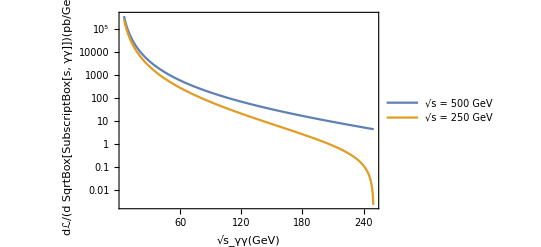

```mathematica
LogPlot[{L[s,500],L[s,250]},{s,5,250},Frame->True,FrameLabel->{Style["√s_γγ(GeV)",Black,FontSize->25],Style["dℒ/(d SqrtBox[SubscriptBox[s, γγ]])(pb/GeV)",Black,FontSize->25]},PlotLegends->{Style["√s = 500 GeV",Black,FontSize->25],Style["√s = 250 GeV",Black,FontSize->25]},FrameTicksStyle->Directive[Black,20],FrameTicks->Automatic ]
```